```mathematica
(*Equations A.6 and A.7  n=2*)
Clear[mh,dmh,mw,dat]
mh:=√2;
dmh:=0;
mw:=mh/2;
r0:=5.7;    (*a[r0]==6.3, a'[r0]==-3, b[r0]==12.0, b'[r0]==-8.6*)  
ar0:=6.3;
dadrr0:=-3; 
br0:=12.0; 
dbdrr0:=-8.6;
rtarget:=0.07;    (*a[rtarget]==0.8, b[rtarget]==-0.05*)
artarget:=0.8; 
brtarget:=-0.05;
rtest:=0.7;          (*a[rtest]==8.05, b[rtest]==-6.3*)
artest:=8.05; 
brtest:=-6.3;
i:=1;
dat=OpenWrite[$TemporaryPrefix<>"pes"];
```

```mathematica
Clear[ar0rand,br0rand];
ar0rand:=RandomReal[{ar0-0.1,ar0+0.1}];
br0rand:=RandomReal[{br0-0.1,br0+0.1}];
sol = NDSolve[{a''[r] -(mh^2+dmh^2)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[r0]==ar0rand,a[rtarget]==0.8,b[r0]==br0rand,b[rtarget]==brtarget},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[r0]==ar0rand,b[r0]==br0rand,a'[r0]==RandomReal[{dadrr0-0.5,dadrr0+0.5}],b'[r0]==RandomReal[{dbdrr0-0.5,dbdrr0+0.5}]}}];
i++;
Write[dat,Evaluate[a[rtest]/.sol]]
(*If[Abs[Evaluate[a[rtest]/.sol]-artest]<0.1(*&&Abs[Evaluate[b[rtest]/.sol]-brtest]<0.1*)(*&&Abs[Evaluate[a[rtarget]/.sol]-artarget]&&Abs[Evaluate[b[rtarget]/.sol]-brtarget]*),a0print:=ar0rand]*)
Close[dat];
```

NDSolve::ndsz: At r == 4.68514, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 3.22125, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.62786, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

```mathematica
a0print
```

a0print

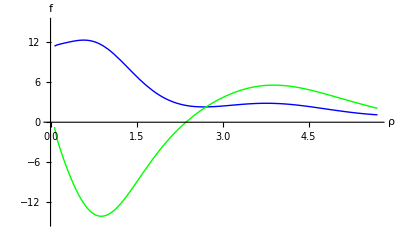

```mathematica
Plot[{Evaluate[a[r] /. sol]/r,Evaluate[b[r] /. sol]/r}, {r,0.07,5.7},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0},PlotRange->{-15,15}]
(*a/r is blue   b/r is green*)
```

```mathematica
(*Equations A.6 and A.7*)
Clear[mh,dmh,mw]
mh:=√2
dmh:=0
mw:=mh/2

sol = NDSolve[{c''[r] -(mh^2+dmh^2)*c[r]+(d[r])^2/(4*r)== 0,d''[r]-mw^2*d[r]-(2*d[r])/r^2+mw^2/r*c[r]*d[r]==0,c[1.41]==10.72,c[0.71]==7.89,d[1.41]==-10.01,d[0.71]==-5.89},{c,d},r, Method->{"Shooting","StartingInitialConditions"->{c[1.41]==10.72,d[1.41]==-10.01,c'[1.41]==-0.12,d'[1.41]==-0.08}}];
```

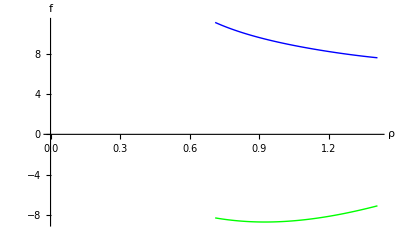

```mathematica
Plot[{Evaluate[c[r] /. sol]/r,Evaluate[d[r] /. sol]/r}, {r,0.71,1.41},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0}]
(*a/r is blue   b/r is green*)
```

```mathematica
Plot[Piecewise[{{Evaluate[c[r] /. sol]/r, {r,0.71,1.41}},{Evaluate[d[r] /. sol]/r, {r,0.71,1.41}},{Evaluate[a[r] /. sol]/r, {r,1.41,7.07}},{Evaluate[b[r] /. sol]/r,{r,1.41,7.07}}}]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Piecewise[{{Evaluate[c[r]/.sol]/r, {r,0.71,1.41}}, {Evaluate[d[r]/.sol]/r, {r,0.71,1.41}}, {Evaluate[a[r]/.sol]/r, {r,1.41,7.07}}, {Evaluate[b[r]/.sol]/r, {r,1.41,7.07}}}]]

```mathematica
(*Archive

a[7.1]==2.1,a[0.4]==27.8,b[0.4]==-1.6,b[7.1]==6.4},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.1]==2.1,b[7.1]==6.4,a'[7.1]==-0.1,b'[7.1]==-0.3}}];




a[7.07]==2.83,a[1.41]==10.72,b[7.07]==7.07,b[1.41]==-10.01},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.07]==2.83,b[7.07]==7.07,a'[7.07]==-0.2,b'[7.07]==-0.4}}];    best so far*)
```